```mathematica
Clear["Global`*"];
```

```mathematica
Df=Min[dAD[ϕ,δ,Χ],dBD[ϕ,δ,Χ]];
Show[ContourPlot3D[Df==2,{ϕ,0,Pi/2},{δ,0,Pi},{Χ,0,Pi},ColorFunction->"Rainbow",AxesLabel->{ϕ,δ,Χ},PlotLegends->Automatic,Mesh->None,ContourStyle->Opacity[0.5],Contours->Automatic,PerformanceGoal->"Quality"],ContourPlot3D[dAB[ϕ,δ]==2,{ϕ,0,Pi/2},{δ,0,Pi},{Χ,0,Pi},AxesLabel->{ϕ,δ,Χ},Axes->True, Ticks-> True,PlotRange->Automatic]]
```

-Graphics3D-

```mathematica
S[ϕ_:0]:=Sin[ϕ]
T[δ_:0]:= Tan[δ]
U[Χ_:0] := Tan[Χ-Pi/4]
Ub[Χ_:0] := Tan[Χ+Pi/4]
```

```mathematica
dAB[ϕ_,δ_] := (4(1-S[ϕ]^2)T[δ]^2)/(S[ϕ]^2+T[δ]^2)
dAD[ϕ_,δ_,Χ_] := (4(S[ϕ] T[δ]+U[Χ])^2)/(1-S[ϕ]^2+T[δ]^2+2S[ϕ] T[δ] U[Χ]+U[Χ]^2)
dBD[ϕ_,δ_,Χ_] := (4(-1+S[ϕ]T[δ]U[Χ])^2)/(1-2S[ϕ]T[δ]U[Χ]+U[Χ]^2-S[ϕ]^2 U[Χ]^2+T[δ]^2 U[Χ]^2)
Df=Min[dAD[ϕ,δ,Χ],dBD[ϕ,δ,Χ]];
```

```mathematica
Plot3D[dAB[ϕ,δ],{ϕ,-Pi/2,Pi/2},{δ,0,Pi},AxesLabel->{ϕ,δ},SphericalRegion->True,Boxed->False,Axes->True, Ticks-> True,PlotRange->Automatic]
```

-Graphics3D-

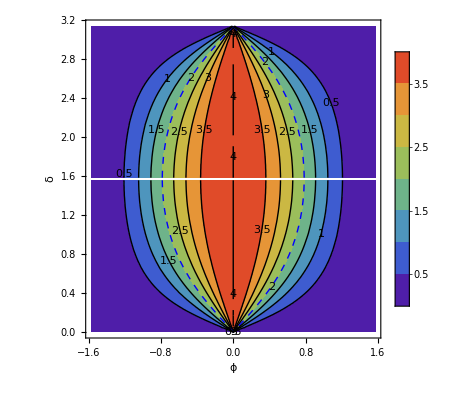

```mathematica
ContourPlot[dAB[ϕ,δ],{ϕ,-Pi/2,Pi/2},{δ,0,Pi},ColorFunction->"Rainbow",FrameLabel->{ϕ,δ},PlotLegends->Automatic,ContourLabels->True,Contours->((*Create a list of {contour value,graphics directive} pairs.
*If a graphics directive is Null,it will have the default*contour line style.*){#,If[#==2,Directive[Thick,Dashed,Blue],Null (*Replace this if you want to change the default*contour graphics directives.*)]}&/@Range[0,4,0.5])
]
```

```mathematica
Manipulate[cp=ContourPlot[dAB[ϕ,δ]==ai,{δ,0,Pi},{ϕ,0,Pi/2},ColorFunction->"Rainbow",FrameLabel->{δ,ϕ},PlotLabel->HoldForm["D_ab"=Dynamic[ai]],ContourLabels->True,PerformanceGoal->"Quality"],{{ai,2,"D_ab"},0.5,3.99999}
]
```

-0.000985749+1.01509 δ-0.0491363 δ^2-0.547774 δ^3+0.384461 δ^4-0.113618 δ^5+0.0120661 δ^6

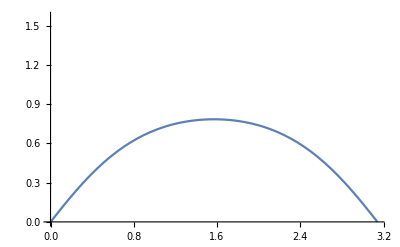

```mathematica
pts=cp[[1,1]][[1]];
ptsfit =Fit[pts,{1,δ,δ^2,δ^3,δ^4,δ^5,δ^6},δ]
Plot[ptsfit,{δ,0,Pi},PlotRange->{{0,Pi},{0,Pi/2}}]
```

```mathematica
Manipulate[
{ContourPlot3D[dAD[ϕ,δ,Χ]==2+ai,{ϕ,0,Pi/2},{δ,0,Pi},{Χ,0,Pi},ColorFunction->"Rainbow",AxesLabel->{ϕ,δ,Χ},PlotLegends->Automatic,Mesh->None,ContourStyle->Opacity[0.5],Contours->Automatic,PerformanceGoal->"Speed",PlotLabel->HoldForm["d_AD"=Dynamic[2+ai]]],ContourPlot3D[dBD[ϕ,δ,Χ]==2+ai,{ϕ,0,Pi/2},{δ,0,Pi},{Χ,0,Pi},ColorFunction->"Rainbow",AxesLabel->{ϕ,δ,Χ},PlotLegends->Automatic,Mesh->None,ContourStyle->Opacity[0.5],Contours->Automatic,PerformanceGoal->"Speed",PlotLabel->HoldForm["d_BD"=Dynamic[2+ai]]]},{{ai,0,"D"},0,1}
]
```

```mathematica
Manipulate[Show[ContourPlot3D[Df==2+ai,{ϕ,0,Pi/2},{δ,0,Pi},{Χ,0,Pi},ColorFunction->"Rainbow",AxesLabel->{ϕ,δ,Χ},PlotLegends->Automatic,Mesh->None,ContourStyle->Opacity[0.5],Contours->Automatic,PerformanceGoal->"Speed",PlotLabel->HoldForm["d_XY"=Dynamic[2+ai]]],ContourPlot3D[dAB[ϕ,δ]==2+ai,{ϕ,0,Pi/2},{δ,0,Pi},{Χ,0,Pi},AxesLabel->{ϕ,δ,Χ},Axes->True, Ticks-> True,PlotRange->Automatic]],{{ai,0.1,"D"},0,1}
]
```